# Chiral potential V

## Using the elliptic functions to determine the chiral potentials

## The potential is constructed to depend on the modulus k explicitly

```mathematica
ClearAll["Global`*"]
```

Helper functions

```mathematica
thesispath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][thesispath,name, format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[q,{q,a,b,(b-a)/(n-1)}];
```

Fit parameters

```mathematica
moisfit1={91,9,51};
moisfit2={13.53,101.76,52.94};
moisfit3={89,12,48};
spinvalues={22.5,18.5,14.5};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
magicpower=2;
A[k_,mois_]:=N[1/(2*#)&/@mois][[k]];
rad[theta_]:=N[theta*π/180];
j[k_,thetadeg_]:={oddspin*Cos[rad[thetadeg]],oddspin*Sin[rad[thetadeg]]}[[k]];
Afactor[spin_,thetadeg_,mois_]:=A[2,mois](1-j[2,thetadeg]/spin)-A[1,mois];
ufactor[spin_,thetadeg_,mois_]:=(A[3,mois]-A[1,mois])/Afactor[spin, thetadeg, mois];
v0factor[spin_,thetadeg_, mois_]:=-(A[1,mois]*j[1,thetadeg])/Afactor[spin,thetadeg,mois];
k[spin_,thetadeg_,mois_]:=√Abs[ufactor[spin,thetadeg,mois]];
period[k_]:=NIntegrate[1/(√(1-k^2 Sin[t]^2)),{t,0,π/2}];
```

Potential

The potential depends on the factors k=√(|u|) and v_0 explicitly

```mathematica
v0const[thetadeg_]:=v0factor[22.5,thetadeg,moisfit1];
uconst[thetadeg_]:=ufactor[22.5,thetadeg,moisfit1];
kconst[thetadeg_]:=k[22.5,thetadeg,moisfit1];
qvalues[k_]:=linspace[-4*period[k],4*period[k],200];
V[q_,spin_,k_,thetadeg_,magicpower_]:=(spin*(spin+1)*k^2+v0const[thetadeg]^2)*Sin[JacobiAmplitude[q,k^magicpower]]^2+(2*spin+1)*v0const[thetadeg]*Cos[JacobiAmplitude[q,k^magicpower]]*√(1-k^2*Sin[JacobiAmplitude[q,k^magicpower]]^2);
dvdq[p_,spin_,k_,thetadeg_,magicpower_]:=D[V[q,spin,k,thetadeg,magicpower],q]/.{q->p};
```

Analysis of the period differences between the potential for θ and θ+π

```mathematica
periodtheta=period[k[22.5,thetadegfit1,moisfit1]];
periodthetapi=period[k[22.5,thetadegfit1+180,moisfit1]];
deltaK=Abs[periodtheta-periodthetapi];
periodlines={Graphics[{Red,Thick,Line[{{-2*period[kconst[thetadegfit1]],-100},{-2*period[kconst[thetadegfit1]],100}}]}],
Graphics[{Red,Thick,Line[{{2*period[kconst[thetadegfit1]],-100},{2*period[kconst[thetadegfit1]],100}}]}],
Graphics[{Blue,DotDashed,Line[{{-2*period[kconst[thetadegfit1+180]],-100},{-2*period[kconst[thetadegfit1+180]],100}}]}],
Graphics[{Blue,DotDashed,Line[{{2*period[kconst[thetadegfit1+180]],-100},{2*period[kconst[thetadegfit1+180]],100}}]}]};
```

Plot the potential V(q,θ) and V(q,θ+π)

```mathematica
potentialPlot=ListLinePlot[{
Table[{q,V[q,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]},{q,qvalues[kconst[thetadegfit1]]}],
Table[{q,V[q+deltaK,22.5,kconst[thetadegfit1+180],thetadegfit1+180,magicpower]},{q,qvalues[kconst[thetadegfit1]]}]},
ImageSize->600,
AspectRatio->0.8,
Frame->True,
Axes->True];
```

Plot the asymmetric potential V_asymm

Requires an offset for the q coordinate for both the θ part and the θ+π part

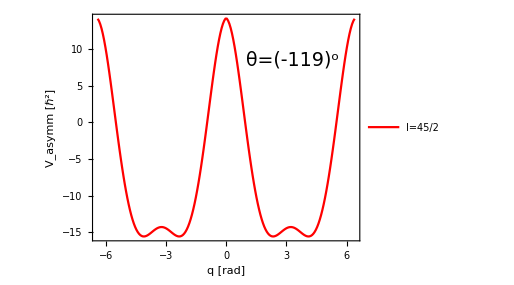

```mathematica
asymmetricplot=ListLinePlot[{
Table[
{q,
If[q<=0,
0.5(V[q+deltaK,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]-V[q-deltaK,22.5,kconst[thetadegfit1+180],thetadegfit1+180,magicpower]),
0.5(V[q-deltaK,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]-V[q+deltaK,22.5,kconst[thetadegfit1+180],thetadegfit1+180,magicpower])]},{q,qvalues[kconst[thetadegfit1]]}]},
ImageSize->380,
AspectRatio->0.75,
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"q [rad]","V_asymm [ℏ^2]"},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
PlotStyle->{Red,Thick},
PlotLegends->Placed[{"I=45/2"},{0.25,0.8}],
Epilog->{Inset[Style[StringTemplate["θ=(``)^o"][thetadegfit1],Black,FontFamily->"Latin Modern Roman",19],Scaled[{0.75,0.8}]]}];
Show[asymmetricplot]
```